# 相関円 （？）

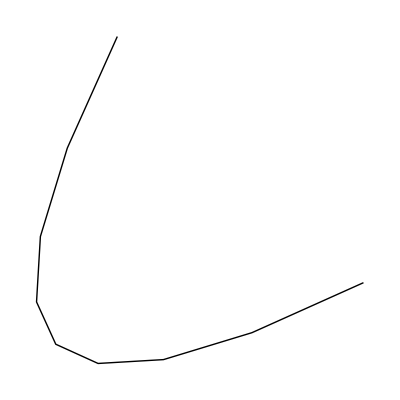

```mathematica
Graphics[BezierCurve[{{1,2},{0,0},{2,1}}]]
```

```mathematica
cp[200]=CirclePoints[1,200];
```

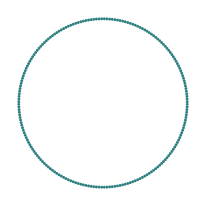

```mathematica
Graphics[{PointSize[0.01],RGBColor[0.18,0.5,0.5],Map[Point,cp[200]]}]
```

```mathematica
randomPair=Table[{RandomInteger[{1,200}],RandomInteger[{1,200}]},{70}];
```

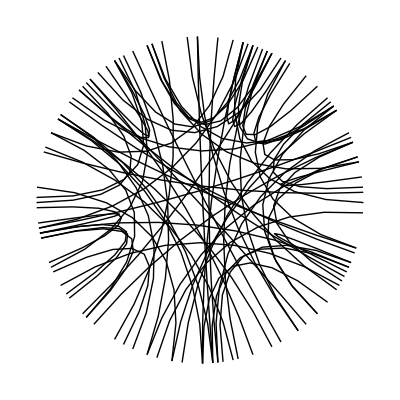

```mathematica
Graphics[bzpair=Map[BezierCurve[{cp[200][[#[[1]]]],{0,0},cp[200][[#[[2]]]]}]&,randomPair]]
```

```mathematica
Graphics[{PointSize[0.01],RGBColor[0.18,0.5,0.5],Map[Point,cp[200]],RGBColor[0.5,0.5,0.5],bzpair}]
```